# Методи на Рунге-Кута за решаване задача на Коши с начално условие

## Задача 3 a) от файла

y’ = y/x+1, x ∈ [1,2]
y(1) = 0

#### РК32 - Формула (1,1)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.3 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.275 k1 = 0.305 k2 = 0.346667 y_точно = 0.278929 истинска грешка = 0.00392944

i = 2 x_i = 1.5 y_i = 0.600833 k1 = 0.350139 k2 = 0.385853 y_точно = 0.608198 истинска грешка = 0.00736433

i = 3 x_i = 1.75 y_i = 0.968829 k1 = 0.388404 k2 = 0.419654 y_точно = 0.979328 истинска грешка = 0.0104983

i = 4 x_i = 2. y_i = 1.37286 k1 = 0.421607 k2 = 0.449385 y_точно = 1.38629 истинска грешка = 0.0134358

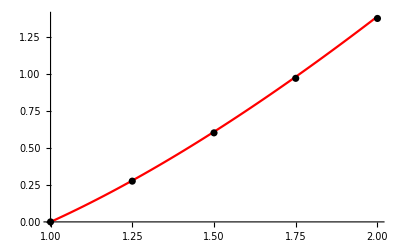

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h,y+k1];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК32 - Формула (1/2,1/2)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.277778 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.277778 k1 = 0.305556 k2 = 0.328283 y_точно = 0.278929 истинска грешка = 0.00115166

i = 2 x_i = 1.5 y_i = 0.606061 k1 = 0.35101 k2 = 0.370241 y_точно = 0.608198 истинска грешка = 0.00213706

i = 3 x_i = 1.75 y_i = 0.976301 k1 = 0.389472 k2 = 0.406138 y_точно = 0.979328 истинска грешка = 0.00302615

i = 4 x_i = 2. y_i = 1.38244 k1 = 0.422805 k2 = 0.437511 y_точно = 1.38629 истинска грешка = 0.00385458

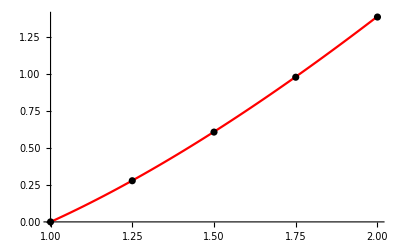

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h/2,y+k1/2];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК32 - Формула (2/3,2/3)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.285714 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.276786 k1 = 0.305357 k2 = 0.334769 y_точно = 0.278929 истинска грешка = 0.00214372

i = 2 x_i = 1.5 y_i = 0.604202 k1 = 0.3507 k2 = 0.3757 y_точно = 0.608198 истинска грешка = 0.00399598

i = 3 x_i = 1.75 y_i = 0.973652 k1 = 0.389093 k2 = 0.410832 y_точно = 0.979328 истинска грешка = 0.00567567

i = 4 x_i = 2. y_i = 1.37905 k1 = 0.422381 k2 = 0.441612 y_точно = 1.38629 истинска грешка = 0.00724492

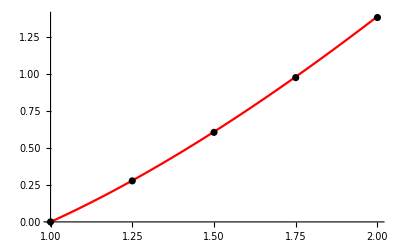

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+2/3 h,y+2/3 k1];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/4 k1+3/4 k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК54 - Формула с 4 междинни точки

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.00390625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.277778 k3 = 0.280864 k4 = 0.306173 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.278909 k1 = 0.305782 k2 = 0.328509 k3 = 0.330575 k4 = 0.351581 y_точно = 0.278929 истинска грешка = 0.0000199741

i = 2 x_i = 1.5 y_i = 0.608165 k1 = 0.351361 k2 = 0.370592 k3 = 0.372071 k4 = 0.390034 y_точно = 0.608198 истинска грешка = 0.0000329341

i = 3 x_i = 1.75 y_i = 0.979285 k1 = 0.389898 k2 = 0.406564 k3 = 0.407676 k4 = 0.42337 y_точно = 0.979328 истинска грешка = 0.0000430257

i = 4 x_i = 2. y_i = 1.38624 k1 = 0.42328 k2 = 0.437986 k3 = 0.438851 k4 = 0.452788 y_точно = 1.38629 истинска грешка = 0.0000517723

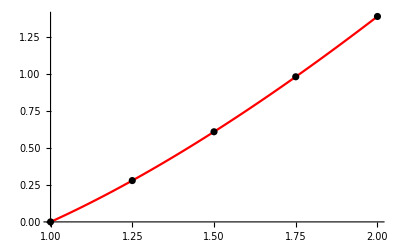

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2," k3 = ", k3, " k4 = ", k4,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

## Задача подобна на б) от домашната

#### Търсим точно решение

търсим частно решение:

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x] - Log[x^2+1]+(2x)/(x^2+1)+4, y[5] == 13}, y[x],x]
```

{{y[x]→(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5}}

#### РК32 - Формула (1,1)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 5. y_i = 13. k1 = 3.53163 k2 = 4.38679 y_точно = 13. истинска грешка = 1.77636×10^-15

i = 1 x_i = 5.25 y_i = 16.9592 k1 = 4.49368 k2 = 5.59072 y_точно = 16.997 истинска грешка = 0.0378394

i = 2 x_i = 5.5 y_i = 22.0014 k1 = 5.72785 k2 = 7.13467 y_точно = 22.0986 истинска грешка = 0.0971793

i = 3 x_i = 5.75 y_i = 28.4327 k1 = 7.31052 k2 = 9.11415 y_точно = 28.6198 истинска грешка = 0.18714

i = 4 x_i = 6. y_i = 36.645 k1 = 9.3396 k2 = 11.6515 y_точно = 36.9653 истинска грешка = 0.320283

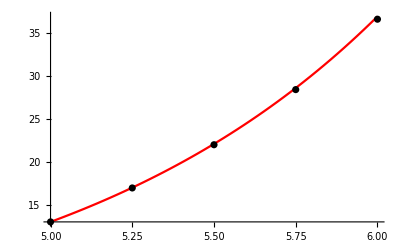

```mathematica
(*въвеждаме условието на задачата*)
a = 5.; b = 6;
x = a;
y = 13.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h,y+k1];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК32-(1/2;1/2)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 5. y_i = 13. k1 = 3.53163 k2 = 3.95903 y_точно = 13. истинска грешка = 1.77636×10^-15

i = 1 x_i = 5.25 y_i = 16.959 k1 = 4.49364 k2 = 5.04199 y_точно = 16.997 истинска грешка = 0.0380182

i = 2 x_i = 5.5 y_i = 22.001 k1 = 5.72775 k2 = 6.431 y_точно = 22.0986 истинска грешка = 0.097571

i = 3 x_i = 5.75 y_i = 28.432 k1 = 7.31036 k2 = 8.21202 y_точно = 28.6198 истинска грешка = 0.187791

i = 4 x_i = 6. y_i = 36.644 k1 = 9.33936 k2 = 10.4952 y_точно = 36.9653 истинска грешка = 0.321253

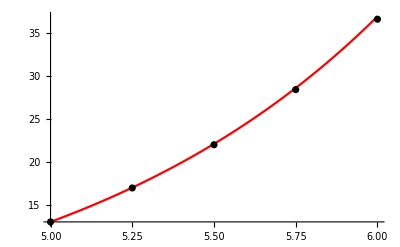

```mathematica
(*въвеждаме условието на задачата*)
a = 5.; b = 6;
x = a;
y = 13.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h/2,y+k1/2];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК32 - Формула (2/3,2/3)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 5. y_i = 13. k1 = 3.53163 k2 = 4.10158 y_точно = 13. истинска грешка = 1.77636×10^-15

i = 1 x_i = 5.25 y_i = 16.9591 k1 = 4.49365 k2 = 5.22486 y_точно = 16.997 истинска грешка = 0.0379579

i = 2 x_i = 5.5 y_i = 22.0011 k1 = 5.72778 k2 = 6.66552 y_точно = 22.0986 истинска грешка = 0.0974391

i = 3 x_i = 5.75 y_i = 28.4322 k1 = 7.31041 k2 = 8.51269 y_точно = 28.6198 истинска грешка = 0.187572

i = 4 x_i = 6. y_i = 36.6444 k1 = 9.33944 k2 = 10.8806 y_точно = 36.9653 истинска грешка = 0.320926

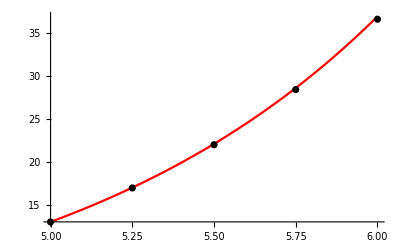

```mathematica
(*въвеждаме условието на задачата*)
a = 5.; b = 6;
x = a;
y = 13.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+2/3 h,y+2/3 k1];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/4 k1+3/4 k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК54 - Формула с 4 междинни точки

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.00390625

i = 0 x_i = 5. y_i = 13. k1 = 3.53163 k2 = 3.95903 k3 = 4.01245 k4 = 4.50699 y_точно = 13. истинска грешка = 1.77636×10^-15

i = 1 x_i = 5.25 y_i = 16.9969 k1 = 4.50311 k2 = 5.05265 k3 = 5.12134 k4 = 5.75706 y_точно = 16.997 истинска грешка = 0.000115847

i = 2 x_i = 5.5 y_i = 22.0983 k1 = 5.75207 k2 = 6.45836 k3 = 6.54664 k4 = 7.36359 y_точно = 22.0986 истинска грешка = 0.000297803

i = 3 x_i = 5.75 y_i = 28.6192 k1 = 7.35716 k2 = 8.26467 k3 = 8.37811 k4 = 9.42769 y_точно = 28.6198 истинска грешка = 0.000574047

i = 4 x_i = 6. y_i = 36.9643 k1 = 9.41943 k2 = 10.5853 k3 = 10.731 k4 = 12.0792 y_точно = 36.9653 истинска грешка = 0.000983435

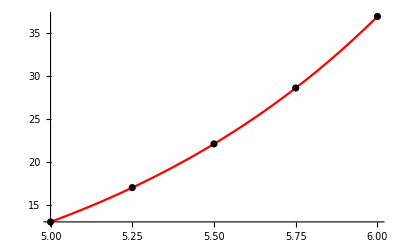

```mathematica
(*въвеждаме условието на задачата*)
a = 5.; b = 6;
x = a;
y = 13.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2," k3 = ", k3, " k4 = ", k4,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК54 - Формула с 4 междинни точки При дадено h

Мрежата е с n = 10. и стъпка h = 0.1

Теоретичната локална  грешка е 0.00001

Теоретичната глобална грешка е 0.0001

i = 0 x_i = 5. y_i = 13. k1 = 1.41265 k2 = 1.48102 k3 = 1.48444 k4 = 1.55659 y_точно = 13. истинска грешка = 1.77636×10^-15

i = 1 x_i = 5.1 y_i = 14.4834 k1 = 1.55648 k2 = 1.63208 k3 = 1.63586 k4 = 1.71565 y_точно = 14.4834 истинска грешка = 1.15607×10^-6

i = 2 x_i = 5.2 y_i = 16.118 k1 = 1.71553 k2 = 1.79913 k3 = 1.80331 k4 = 1.89153 y_точно = 16.118 истинска грешка = 2.55651×10^-6

i = 3 x_i = 5.3 y_i = 17.92 k1 = 1.8914 k2 = 1.98384 k3 = 1.98846 k4 = 2.08601 y_точно = 17.92 истинска грешка = 4.23988×10^-6

i = 4 x_i = 5.4 y_i = 19.907 k1 = 2.08586 k2 = 2.18806 k3 = 2.19317 k4 = 2.30102 y_точно = 19.907 истинска грешка = 6.25016×10^-6

i = 5 x_i = 5.5 y_i = 22.0986 k1 = 2.30086 k2 = 2.41385 k3 = 2.4195 k4 = 2.53873 y_точно = 22.0986 истинска грешка = 8.63745×10^-6

i = 6 x_i = 5.6 y_i = 24.5163 k1 = 2.53855 k2 = 2.66346 k3 = 2.66971 k4 = 2.80152 y_точно = 24.5163 истинска грешка = 0.0000114588

i = 7 x_i = 5.7 y_i = 27.184 k1 = 2.80132 k2 = 2.93941 k3 = 2.94632 k4 = 3.09202 y_точно = 27.184 истинска грешка = 0.000014779

i = 8 x_i = 5.8 y_i = 30.1282 k1 = 3.0918 k2 = 3.24445 k3 = 3.25209 k4 = 3.41315 y_точно = 30.1282 истинска грешка = 0.0000186718

i = 9 x_i = 5.9 y_i = 33.3778 k1 = 3.41291 k2 = 3.58166 k3 = 3.59009 k4 = 3.76813 y_точно = 33.3779 истинска грешка = 0.0000232208

i = 10 x_i = 6. y_i = 36.9653 k1 = 3.76787 k2 = 3.95439 k3 = 3.96372 k4 = 4.16052 y_точно = 36.9653 истинска грешка = 0.0000285211

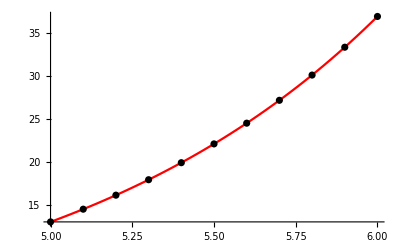

```mathematica
(*въвеждаме условието на задачата*)
a = 5.; b = 6;
x = a;
y = 13.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
(*съставяме мрежата*)
h = 0.1; n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2," k3 = ", k3, " k4 = ", k4,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

#### РК54 - Формула с 4 междинни точки За достигане на предварително зададена точност

```mathematica
Clear[n]
Reduce[((b-a)/n)^4<= 10^-10, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-316.228||n≥316.228

Мрежата е с n = 317 и стъпка h = 0.00315457

Теоретичната локална  грешка е 3.12395×10^-13

Теоретичната глобална грешка е 9.90291×10^-11

i = 0 x_i = 5. y_i = 13. k1 = 0.0445632 k2 = 0.0446312 k3 = 0.0446313 k4 = 0.0446994 y_точно = 13. истинска грешка = 1.77636×10^-15

i = 1 x_i = 5.00315 y_i = 13.0446 k1 = 0.0446994 k2 = 0.0447676 k3 = 0.0447678 k4 = 0.0448361 y_точно = 13.0446 истинска грешка = 3.19744×10^-14

i = 2 x_i = 5.00631 y_i = 13.0894 k1 = 0.0448361 k2 = 0.0449046 k3 = 0.0449047 k4 = 0.0449732 y_точно = 13.0894 истинска грешка = 7.10543×10^-14

i = 3 x_i = 5.00946 y_i = 13.1343 k1 = 0.0449732 k2 = 0.0450419 k3 = 0.045042 k4 = 0.0451108 y_точно = 13.1343 истинска грешка = 1.04805×10^-13

i = 4 x_i = 5.01262 y_i = 13.1793 k1 = 0.0451108 k2 = 0.0451797 k3 = 0.0451798 k4 = 0.0452488 y_точно = 13.1793 истинска грешка = 1.40332×10^-13

i = 5 x_i = 5.01577 y_i = 13.2245 k1 = 0.0452488 k2 = 0.0453179 k3 = 0.045318 k4 = 0.0453872 y_точно = 13.2245 истинска грешка = 1.74083×10^-13

i = 6 x_i = 5.01893 y_i = 13.2698 k1 = 0.0453872 k2 = 0.0454566 k3 = 0.0454567 k4 = 0.0455261 y_точно = 13.2698 истинска грешка = 2.13163×10^-13

i = 7 x_i = 5.02208 y_i = 13.3153 k1 = 0.0455261 k2 = 0.0455957 k3 = 0.0455958 k4 = 0.0456654 y_точно = 13.3153 истинска грешка = 2.4869×10^-13

i = 8 x_i = 5.02524 y_i = 13.3609 k1 = 0.0456654 k2 = 0.0457352 k3 = 0.0457353 k4 = 0.0458052 y_точно = 13.3609 истинска грешка = 2.8777×10^-13

i = 9 x_i = 5.02839 y_i = 13.4066 k1 = 0.0458052 k2 = 0.0458752 k3 = 0.0458753 k4 = 0.0459454 y_точно = 13.4066 истинска грешка = 3.23297×10^-13

i = 10 x_i = 5.03155 y_i = 13.4525 k1 = 0.0459454 k2 = 0.0460156 k3 = 0.0460158 k4 = 0.0460861 y_точно = 13.4525 истинска грешка = 3.62377×10^-13

i = 11 x_i = 5.0347 y_i = 13.4985 k1 = 0.0460861 k2 = 0.0461565 k3 = 0.0461566 k4 = 0.0462272 y_точно = 13.4985 истинска грешка = 3.96128×10^-13

i = 12 x_i = 5.03785 y_i = 13.5447 k1 = 0.0462272 k2 = 0.0462979 k3 = 0.046298 k4 = 0.0463687 y_точно = 13.5447 истинска грешка = 4.35207×10^-13

i = 13 x_i = 5.04101 y_i = 13.591 k1 = 0.0463687 k2 = 0.0464396 k3 = 0.0464397 k4 = 0.0465107 y_точно = 13.591 истинска грешка = 4.74287×10^-13

i = 14 x_i = 5.04416 y_i = 13.6374 k1 = 0.0465107 k2 = 0.0465819 k3 = 0.046582 k4 = 0.0466532 y_точно = 13.6374 истинска грешка = 5.09814×10^-13

i = 15 x_i = 5.04732 y_i = 13.684 k1 = 0.0466532 k2 = 0.0467245 k3 = 0.0467247 k4 = 0.0467961 y_точно = 13.684 истинска грешка = 5.47118×10^-13

i = 16 x_i = 5.05047 y_i = 13.7307 k1 = 0.0467961 k2 = 0.0468677 k3 = 0.0468678 k4 = 0.0469395 y_точно = 13.7307 истинска грешка = 5.8975×10^-13

i = 17 x_i = 5.05363 y_i = 13.7776 k1 = 0.0469395 k2 = 0.0470113 k3 = 0.0470114 k4 = 0.0470833 y_точно = 13.7776 истинска грешка = 6.2883×10^-13

i = 18 x_i = 5.05678 y_i = 13.8246 k1 = 0.0470833 k2 = 0.0471553 k3 = 0.0471554 k4 = 0.0472276 y_точно = 13.8246 истинска грешка = 6.6791×10^-13

i = 19 x_i = 5.05994 y_i = 13.8718 k1 = 0.0472276 k2 = 0.0472998 k3 = 0.0472999 k4 = 0.0473723 y_точно = 13.8718 истинска грешка = 7.05214×10^-13

i = 20 x_i = 5.06309 y_i = 13.9191 k1 = 0.0473723 k2 = 0.0474448 k3 = 0.0474449 k4 = 0.0475175 y_точно = 13.9191 истинска грешка = 7.47846×10^-13

i = 21 x_i = 5.06625 y_i = 13.9665 k1 = 0.0475175 k2 = 0.0475902 k3 = 0.0475903 k4 = 0.0476632 y_точно = 13.9665 истинска грешка = 7.88702×10^-13

i = 22 x_i = 5.0694 y_i = 14.0141 k1 = 0.0476632 k2 = 0.0477361 k3 = 0.0477362 k4 = 0.0478093 y_точно = 14.0141 истинска грешка = 8.26006×10^-13

i = 23 x_i = 5.07256 y_i = 14.0618 k1 = 0.0478093 k2 = 0.0478825 k3 = 0.0478826 k4 = 0.0479559 y_точно = 14.0618 истинска грешка = 8.68638×10^-13

i = 24 x_i = 5.07571 y_i = 14.1097 k1 = 0.0479559 k2 = 0.0480293 k3 = 0.0480294 k4 = 0.0481029 y_точно = 14.1097 истинска грешка = 9.07718×10^-13

i = 25 x_i = 5.07886 y_i = 14.1577 k1 = 0.0481029 k2 = 0.0481766 k3 = 0.0481767 k4 = 0.0482504 y_точно = 14.1577 истинска грешка = 9.48575×10^-13

i = 26 x_i = 5.08202 y_i = 14.2059 k1 = 0.0482504 k2 = 0.0483243 k3 = 0.0483244 k4 = 0.0483984 y_точно = 14.2059 истинска грешка = 9.89431×10^-13

i = 27 x_i = 5.08517 y_i = 14.2542 k1 = 0.0483984 k2 = 0.0484725 k3 = 0.0484726 k4 = 0.0485469 y_точно = 14.2542 истинска грешка = 1.03206×10^-12

i = 28 x_i = 5.08833 y_i = 14.3027 k1 = 0.0485469 k2 = 0.0486212 k3 = 0.0486213 k4 = 0.0486958 y_точно = 14.3027 истинска грешка = 1.07292×10^-12

i = 29 x_i = 5.09148 y_i = 14.3513 k1 = 0.0486958 k2 = 0.0487704 k3 = 0.0487705 k4 = 0.0488452 y_точно = 14.3513 истинска грешка = 1.11378×10^-12

i = 30 x_i = 5.09464 y_i = 14.4001 k1 = 0.0488452 k2 = 0.04892 k3 = 0.0489201 k4 = 0.0489951 y_точно = 14.4001 истинска грешка = 1.15641×10^-12

i = 31 x_i = 5.09779 y_i = 14.449 k1 = 0.0489951 k2 = 0.0490701 k3 = 0.0490703 k4 = 0.0491454 y_точно = 14.449 истинска грешка = 1.19726×10^-12

i = 32 x_i = 5.10095 y_i = 14.4981 k1 = 0.0491454 k2 = 0.0492207 k3 = 0.0492209 k4 = 0.0492963 y_точно = 14.4981 истинска грешка = 1.24167×10^-12

i = 33 x_i = 5.1041 y_i = 14.5473 k1 = 0.0492963 k2 = 0.0493718 k3 = 0.0493719 k4 = 0.0494476 y_точно = 14.5473 истинска грешка = 1.28608×10^-12

i = 34 x_i = 5.10726 y_i = 14.5967 k1 = 0.0494476 k2 = 0.0495234 k3 = 0.0495235 k4 = 0.0495994 y_точно = 14.5967 истинска грешка = 1.32339×10^-12

i = 35 x_i = 5.11041 y_i = 14.6462 k1 = 0.0495994 k2 = 0.0496754 k3 = 0.0496755 k4 = 0.0497517 y_точно = 14.6462 истинска грешка = 1.37135×10^-12

i = 36 x_i = 5.11356 y_i = 14.6959 k1 = 0.0497517 k2 = 0.0498279 k3 = 0.049828 k4 = 0.0499044 y_точно = 14.6959 истинска грешка = 1.41398×10^-12

i = 37 x_i = 5.11672 y_i = 14.7457 k1 = 0.0499044 k2 = 0.0499809 k3 = 0.049981 k4 = 0.0500577 y_точно = 14.7457 истинска грешка = 1.45839×10^-12

i = 38 x_i = 5.11987 y_i = 14.7957 k1 = 0.0500577 k2 = 0.0501344 k3 = 0.0501345 k4 = 0.0502114 y_точно = 14.7957 истинска грешка = 1.50102×10^-12

i = 39 x_i = 5.12303 y_i = 14.8458 k1 = 0.0502114 k2 = 0.0502884 k3 = 0.0502885 k4 = 0.0503656 y_точно = 14.8458 истинска грешка = 1.54721×10^-12

i = 40 x_i = 5.12618 y_i = 14.8961 k1 = 0.0503656 k2 = 0.0504428 k3 = 0.050443 k4 = 0.0505203 y_точно = 14.8961 истинска грешка = 1.59162×10^-12

i = 41 x_i = 5.12934 y_i = 14.9466 k1 = 0.0505203 k2 = 0.0505978 k3 = 0.0505979 k4 = 0.0506755 y_точно = 14.9466 истинска грешка = 1.63602×10^-12

i = 42 x_i = 5.13249 y_i = 14.9972 k1 = 0.0506755 k2 = 0.0507533 k3 = 0.0507534 k4 = 0.0508312 y_точно = 14.9972 истинска грешка = 1.68221×10^-12

i = 43 x_i = 5.13565 y_i = 15.0479 k1 = 0.0508312 k2 = 0.0509092 k3 = 0.0509093 k4 = 0.0509874 y_точно = 15.0479 истинска грешка = 1.73017×10^-12

i = 44 x_i = 5.1388 y_i = 15.0988 k1 = 0.0509874 k2 = 0.0510656 k3 = 0.0510658 k4 = 0.0511441 y_точно = 15.0988 истинска грешка = 1.77103×10^-12

i = 45 x_i = 5.14196 y_i = 15.1499 k1 = 0.0511441 k2 = 0.0512226 k3 = 0.0512227 k4 = 0.0513013 y_точно = 15.1499 истинска грешка = 1.81899×10^-12

i = 46 x_i = 5.14511 y_i = 15.2011 k1 = 0.0513013 k2 = 0.05138 k3 = 0.0513801 k4 = 0.051459 y_точно = 15.2011 истинска грешка = 1.86517×10^-12

i = 47 x_i = 5.14826 y_i = 15.2525 k1 = 0.051459 k2 = 0.0515379 k3 = 0.0515381 k4 = 0.0516172 y_точно = 15.2525 истинска грешка = 1.90781×10^-12

i = 48 x_i = 5.15142 y_i = 15.304 k1 = 0.0516172 k2 = 0.0516964 k3 = 0.0516965 k4 = 0.0517758 y_точно = 15.304 истинска грешка = 1.95755×10^-12

i = 49 x_i = 5.15457 y_i = 15.3557 k1 = 0.0517758 k2 = 0.0518553 k3 = 0.0518554 k4 = 0.051935 y_точно = 15.3557 истинска грешка = 2.00373×10^-12

i = 50 x_i = 5.15773 y_i = 15.4076 k1 = 0.051935 k2 = 0.0520148 k3 = 0.0520149 k4 = 0.0520947 y_точно = 15.4076 истинска грешка = 2.05169×10^-12

i = 51 x_i = 5.16088 y_i = 15.4596 k1 = 0.0520947 k2 = 0.0521747 k3 = 0.0521748 k4 = 0.0522549 y_точно = 15.4596 истинска грешка = 2.09965×10^-12

i = 52 x_i = 5.16404 y_i = 15.5118 k1 = 0.0522549 k2 = 0.0523352 k3 = 0.0523353 k4 = 0.0524157 y_точно = 15.5118 истинска грешка = 2.14584×10^-12

i = 53 x_i = 5.16719 y_i = 15.5641 k1 = 0.0524157 k2 = 0.0524961 k3 = 0.0524963 k4 = 0.0525769 y_точно = 15.5641 истинска грешка = 2.1938×10^-12

i = 54 x_i = 5.17035 y_i = 15.6166 k1 = 0.0525769 k2 = 0.0526576 k3 = 0.0526577 k4 = 0.0527386 y_точно = 15.6166 истинска грешка = 2.24176×10^-12

i = 55 x_i = 5.1735 y_i = 15.6693 k1 = 0.0527386 k2 = 0.0528196 k3 = 0.0528197 k4 = 0.0529009 y_точно = 15.6693 истинска грешка = 2.28795×10^-12

i = 56 x_i = 5.17666 y_i = 15.7221 k1 = 0.0529009 k2 = 0.0529821 k3 = 0.0529823 k4 = 0.0530636 y_точно = 15.7221 истинска грешка = 2.33591×10^-12

i = 57 x_i = 5.17981 y_i = 15.7751 k1 = 0.0530636 k2 = 0.0531451 k3 = 0.0531453 k4 = 0.0532269 y_точно = 15.7751 истинска грешка = 2.39098×10^-12

i = 58 x_i = 5.18297 y_i = 15.8282 k1 = 0.0532269 k2 = 0.0533087 k3 = 0.0533088 k4 = 0.0533907 y_точно = 15.8282 истинска грешка = 2.43894×10^-12

i = 59 x_i = 5.18612 y_i = 15.8815 k1 = 0.0533907 k2 = 0.0534728 k3 = 0.0534729 k4 = 0.053555 y_точно = 15.8815 истинска грешка = 2.4869×10^-12

i = 60 x_i = 5.18927 y_i = 15.935 k1 = 0.053555 k2 = 0.0536373 k3 = 0.0536375 k4 = 0.0537199 y_точно = 15.935 истинска грешка = 2.53841×10^-12

i = 61 x_i = 5.19243 y_i = 15.9886 k1 = 0.0537199 k2 = 0.0538024 k3 = 0.0538026 k4 = 0.0538853 y_точно = 15.9886 истинска грешка = 2.58815×10^-12

i = 62 x_i = 5.19558 y_i = 16.0424 k1 = 0.0538853 k2 = 0.0539681 k3 = 0.0539682 k4 = 0.0540512 y_точно = 16.0424 истинска грешка = 2.63611×10^-12

i = 63 x_i = 5.19874 y_i = 16.0964 k1 = 0.0540512 k2 = 0.0541342 k3 = 0.0541344 k4 = 0.0542176 y_точно = 16.0964 истинска грешка = 2.6894×10^-12

i = 64 x_i = 5.20189 y_i = 16.1505 k1 = 0.0542176 k2 = 0.0543009 k3 = 0.054301 k4 = 0.0543845 y_точно = 16.1505 истинска грешка = 2.73559×10^-12

i = 65 x_i = 5.20505 y_i = 16.2048 k1 = 0.0543845 k2 = 0.0544681 k3 = 0.0544683 k4 = 0.054552 y_точно = 16.2048 истинска грешка = 2.79243×10^-12

i = 66 x_i = 5.2082 y_i = 16.2593 k1 = 0.054552 k2 = 0.0546359 k3 = 0.054636 k4 = 0.05472 y_точно = 16.2593 истинска грешка = 2.84217×10^-12

i = 67 x_i = 5.21136 y_i = 16.3139 k1 = 0.05472 k2 = 0.0548042 k3 = 0.0548043 k4 = 0.0548886 y_точно = 16.3139 истинска грешка = 2.90257×10^-12

i = 68 x_i = 5.21451 y_i = 16.3687 k1 = 0.0548886 k2 = 0.054973 k3 = 0.0549731 k4 = 0.0550576 y_точно = 16.3687 истинска грешка = 2.94875×10^-12

i = 69 x_i = 5.21767 y_i = 16.4237 k1 = 0.0550576 k2 = 0.0551423 k3 = 0.0551424 k4 = 0.0552273 y_точно = 16.4237 истинска грешка = 3.0056×10^-12

i = 70 x_i = 5.22082 y_i = 16.4789 k1 = 0.0552273 k2 = 0.0553122 k3 = 0.0553123 k4 = 0.0553974 y_точно = 16.4789 истинска грешка = 3.05533×10^-12

i = 71 x_i = 5.22397 y_i = 16.5342 k1 = 0.0553974 k2 = 0.0554826 k3 = 0.0554828 k4 = 0.0555681 y_точно = 16.5342 истинска грешка = 3.11218×10^-12

i = 72 x_i = 5.22713 y_i = 16.5897 k1 = 0.0555681 k2 = 0.0556536 k3 = 0.0556537 k4 = 0.0557394 y_точно = 16.5897 истинска грешка = 3.16902×10^-12

i = 73 x_i = 5.23028 y_i = 16.6453 k1 = 0.0557394 k2 = 0.0558251 k3 = 0.0558252 k4 = 0.0559111 y_точно = 16.6453 истинска грешка = 3.22231×10^-12

i = 74 x_i = 5.23344 y_i = 16.7011 k1 = 0.0559111 k2 = 0.0559972 k3 = 0.0559973 k4 = 0.0560835 y_точно = 16.7011 истинска грешка = 3.27915×10^-12

i = 75 x_i = 5.23659 y_i = 16.7571 k1 = 0.0560835 k2 = 0.0561698 k3 = 0.0561699 k4 = 0.0562563 y_точно = 16.7571 истинска грешка = 3.33245×10^-12

i = 76 x_i = 5.23975 y_i = 16.8133 k1 = 0.0562563 k2 = 0.0563429 k3 = 0.056343 k4 = 0.0564298 y_точно = 16.8133 истинска грешка = 3.38929×10^-12

i = 77 x_i = 5.2429 y_i = 16.8696 k1 = 0.0564298 k2 = 0.0565166 k3 = 0.0565167 k4 = 0.0566037 y_точно = 16.8696 истинска грешка = 3.44968×10^-12

i = 78 x_i = 5.24606 y_i = 16.9262 k1 = 0.0566037 k2 = 0.0566909 k3 = 0.056691 k4 = 0.0567783 y_точно = 16.9262 истинска грешка = 3.50298×10^-12

i = 79 x_i = 5.24921 y_i = 16.9828 k1 = 0.0567783 k2 = 0.0568657 k3 = 0.0568658 k4 = 0.0569533 y_точно = 16.9828 истинска грешка = 3.55627×10^-12

i = 80 x_i = 5.25237 y_i = 17.0397 k1 = 0.0569533 k2 = 0.057041 k3 = 0.0570412 k4 = 0.057129 y_точно = 17.0397 истинска грешка = 3.61311×10^-12

i = 81 x_i = 5.25552 y_i = 17.0968 k1 = 0.057129 k2 = 0.0572169 k3 = 0.0572171 k4 = 0.0573052 y_точно = 17.0968 истинска грешка = 3.66995×10^-12

i = 82 x_i = 5.25868 y_i = 17.154 k1 = 0.0573052 k2 = 0.0573934 k3 = 0.0573936 k4 = 0.0574819 y_точно = 17.154 истинска грешка = 3.7268×10^-12

i = 83 x_i = 5.26183 y_i = 17.2114 k1 = 0.0574819 k2 = 0.0575705 k3 = 0.0575706 k4 = 0.0576592 y_точно = 17.2114 истинска грешка = 3.77653×10^-12

i = 84 x_i = 5.26498 y_i = 17.2689 k1 = 0.0576592 k2 = 0.057748 k3 = 0.0577482 k4 = 0.0578371 y_точно = 17.2689 истинска грешка = 3.83693×10^-12

i = 85 x_i = 5.26814 y_i = 17.3267 k1 = 0.0578371 k2 = 0.0579262 k3 = 0.0579263 k4 = 0.0580156 y_точно = 17.3267 истинска грешка = 3.89377×10^-12

i = 86 x_i = 5.27129 y_i = 17.3846 k1 = 0.0580156 k2 = 0.0581049 k3 = 0.0581051 k4 = 0.0581946 y_точно = 17.3846 истинска грешка = 3.96128×10^-12

i = 87 x_i = 5.27445 y_i = 17.4427 k1 = 0.0581946 k2 = 0.0582842 k3 = 0.0582844 k4 = 0.0583742 y_точно = 17.4427 истинска грешка = 4.01812×10^-12

i = 88 x_i = 5.2776 y_i = 17.501 k1 = 0.0583742 k2 = 0.0584641 k3 = 0.0584642 k4 = 0.0585543 y_точно = 17.501 истинска грешка = 4.07852×10^-12

i = 89 x_i = 5.28076 y_i = 17.5595 k1 = 0.0585543 k2 = 0.0586445 k3 = 0.0586447 k4 = 0.058735 y_точно = 17.5595 истинска грешка = 4.13536×10^-12

i = 90 x_i = 5.28391 y_i = 17.6181 k1 = 0.058735 k2 = 0.0588255 k3 = 0.0588257 k4 = 0.0589163 y_точно = 17.6181 истинска грешка = 4.19931×10^-12

i = 91 x_i = 5.28707 y_i = 17.6769 k1 = 0.0589163 k2 = 0.0590071 k3 = 0.0590073 k4 = 0.0590982 y_точно = 17.6769 истинска грешка = 4.2597×10^-12

i = 92 x_i = 5.29022 y_i = 17.7359 k1 = 0.0590982 k2 = 0.0591893 k3 = 0.0591894 k4 = 0.0592806 y_точно = 17.7359 истинска грешка = 4.3201×10^-12

i = 93 x_i = 5.29338 y_i = 17.7951 k1 = 0.0592806 k2 = 0.059372 k3 = 0.0593722 k4 = 0.0594637 y_точно = 17.7951 истинска грешка = 4.3805×10^-12

i = 94 x_i = 5.29653 y_i = 17.8545 k1 = 0.0594637 k2 = 0.0595553 k3 = 0.0595555 k4 = 0.0596473 y_точно = 17.8545 истинска грешка = 4.44089×10^-12

i = 95 x_i = 5.29968 y_i = 17.9141 k1 = 0.0596473 k2 = 0.0597392 k3 = 0.0597394 k4 = 0.0598315 y_точно = 17.9141 истинска грешка = 4.50129×10^-12

i = 96 x_i = 5.30284 y_i = 17.9738 k1 = 0.0598315 k2 = 0.0599237 k3 = 0.0599238 k4 = 0.0600162 y_точно = 17.9738 истинска грешка = 4.56524×10^-12

i = 97 x_i = 5.30599 y_i = 18.0337 k1 = 0.0600162 k2 = 0.0601088 k3 = 0.0601089 k4 = 0.0602016 y_точно = 18.0337 истинска грешка = 4.62563×10^-12

i = 98 x_i = 5.30915 y_i = 18.0938 k1 = 0.0602016 k2 = 0.0602944 k3 = 0.0602946 k4 = 0.0603875 y_точно = 18.0938 истинска грешка = 4.68958×10^-12

i = 99 x_i = 5.3123 y_i = 18.1541 k1 = 0.0603875 k2 = 0.0604807 k3 = 0.0604808 k4 = 0.0605741 y_точно = 18.1541 истинска грешка = 4.75353×10^-12

i = 100 x_i = 5.31546 y_i = 18.2146 k1 = 0.0605741 k2 = 0.0606675 k3 = 0.0606677 k4 = 0.0607612 y_точно = 18.2146 истинска грешка = 4.81748×10^-12

i = 101 x_i = 5.31861 y_i = 18.2753 k1 = 0.0607612 k2 = 0.0608549 k3 = 0.0608551 k4 = 0.0609489 y_точно = 18.2753 истинска грешка = 4.88143×10^-12

i = 102 x_i = 5.32177 y_i = 18.3361 k1 = 0.0609489 k2 = 0.061043 k3 = 0.0610431 k4 = 0.0611373 y_точно = 18.3361 истинска грешка = 4.94182×10^-12

i = 103 x_i = 5.32492 y_i = 18.3972 k1 = 0.0611373 k2 = 0.0612316 k3 = 0.0612317 k4 = 0.0613262 y_точно = 18.3972 истинска грешка = 5.00577×10^-12

i = 104 x_i = 5.32808 y_i = 18.4584 k1 = 0.0613262 k2 = 0.0614208 k3 = 0.0614209 k4 = 0.0615157 y_точно = 18.4584 истинска грешка = 5.07328×10^-12

i = 105 x_i = 5.33123 y_i = 18.5198 k1 = 0.0615157 k2 = 0.0616106 k3 = 0.0616108 k4 = 0.0617058 y_точно = 18.5198 истинска грешка = 5.13722×10^-12

i = 106 x_i = 5.33438 y_i = 18.5814 k1 = 0.0617058 k2 = 0.061801 k3 = 0.0618012 k4 = 0.0618965 y_точно = 18.5814 истинска грешка = 5.20117×10^-12

i = 107 x_i = 5.33754 y_i = 18.6432 k1 = 0.0618965 k2 = 0.0619921 k3 = 0.0619922 k4 = 0.0620879 y_точно = 18.6432 истинска грешка = 5.26512×10^-12

i = 108 x_i = 5.34069 y_i = 18.7052 k1 = 0.0620879 k2 = 0.0621837 k3 = 0.0621838 k4 = 0.0622798 y_точно = 18.7052 истинска грешка = 5.33262×10^-12

i = 109 x_i = 5.34385 y_i = 18.7674 k1 = 0.0622798 k2 = 0.0623759 k3 = 0.0623761 k4 = 0.0624724 y_точно = 18.7674 истинска грешка = 5.40012×10^-12

i = 110 x_i = 5.347 y_i = 18.8298 k1 = 0.0624724 k2 = 0.0625688 k3 = 0.0625689 k4 = 0.0626655 y_точно = 18.8298 истинска грешка = 5.46407×10^-12

i = 111 x_i = 5.35016 y_i = 18.8924 k1 = 0.0626655 k2 = 0.0627622 k3 = 0.0627624 k4 = 0.0628593 y_точно = 18.8924 истинска грешка = 5.53513×10^-12

i = 112 x_i = 5.35331 y_i = 18.9551 k1 = 0.0628593 k2 = 0.0629563 k3 = 0.0629565 k4 = 0.0630537 y_точно = 18.9551 истинска грешка = 5.60263×10^-12

i = 113 x_i = 5.35647 y_i = 19.0181 k1 = 0.0630537 k2 = 0.063151 k3 = 0.0631512 k4 = 0.0632487 y_точно = 19.0181 истинска грешка = 5.66658×10^-12

i = 114 x_i = 5.35962 y_i = 19.0812 k1 = 0.0632487 k2 = 0.0633463 k3 = 0.0633465 k4 = 0.0634443 y_точно = 19.0812 истинска грешка = 5.73408×10^-12

i = 115 x_i = 5.36278 y_i = 19.1446 k1 = 0.0634443 k2 = 0.0635422 k3 = 0.0635424 k4 = 0.0636405 y_точно = 19.1446 истинска грешка = 5.80158×10^-12

i = 116 x_i = 5.36593 y_i = 19.2081 k1 = 0.0636405 k2 = 0.0637388 k3 = 0.063739 k4 = 0.0638374 y_точно = 19.2081 истинска грешка = 5.87264×10^-12

i = 117 x_i = 5.36909 y_i = 19.2719 k1 = 0.0638374 k2 = 0.063936 k3 = 0.0639361 k4 = 0.0640349 y_точно = 19.2719 истинска грешка = 5.94369×10^-12

i = 118 x_i = 5.37224 y_i = 19.3358 k1 = 0.0640349 k2 = 0.0641338 k3 = 0.0641339 k4 = 0.064233 y_точно = 19.3358 истинска грешка = 6.01474×10^-12

i = 119 x_i = 5.37539 y_i = 19.3999 k1 = 0.064233 k2 = 0.0643322 k3 = 0.0643324 k4 = 0.0644317 y_точно = 19.3999 истинска грешка = 6.08225×10^-12

i = 120 x_i = 5.37855 y_i = 19.4643 k1 = 0.0644317 k2 = 0.0645313 k3 = 0.0645314 k4 = 0.0646311 y_точно = 19.4643 истинска грешка = 6.1533×10^-12

i = 121 x_i = 5.3817 y_i = 19.5288 k1 = 0.0646311 k2 = 0.0647309 k3 = 0.0647311 k4 = 0.0648311 y_точно = 19.5288 истинска грешка = 6.22791×10^-12

i = 122 x_i = 5.38486 y_i = 19.5935 k1 = 0.0648311 k2 = 0.0649313 k3 = 0.0649314 k4 = 0.0650317 y_точно = 19.5935 истинска грешка = 6.29896×10^-12

i = 123 x_i = 5.38801 y_i = 19.6585 k1 = 0.0650317 k2 = 0.0651322 k3 = 0.0651324 k4 = 0.065233 y_точно = 19.6585 истинска грешка = 6.37002×10^-12

i = 124 x_i = 5.39117 y_i = 19.7236 k1 = 0.065233 k2 = 0.0653338 k3 = 0.065334 k4 = 0.0654349 y_точно = 19.7236 истинска грешка = 6.44107×10^-12

i = 125 x_i = 5.39432 y_i = 19.7889 k1 = 0.0654349 k2 = 0.0655361 k3 = 0.0655362 k4 = 0.0656375 y_точно = 19.7889 истинска грешка = 6.51212×10^-12

i = 126 x_i = 5.39748 y_i = 19.8545 k1 = 0.0656375 k2 = 0.0657389 k3 = 0.0657391 k4 = 0.0658407 y_точно = 19.8545 истинска грешка = 6.58673×10^-12

i = 127 x_i = 5.40063 y_i = 19.9202 k1 = 0.0658407 k2 = 0.0659425 k3 = 0.0659426 k4 = 0.0660445 y_точно = 19.9202 истинска грешка = 6.66134×10^-12

i = 128 x_i = 5.40379 y_i = 19.9861 k1 = 0.0660445 k2 = 0.0661466 k3 = 0.0661468 k4 = 0.066249 y_точно = 19.9861 истинска грешка = 6.73595×10^-12

i = 129 x_i = 5.40694 y_i = 20.0523 k1 = 0.066249 k2 = 0.0663514 k3 = 0.0663516 k4 = 0.0664542 y_точно = 20.0523 истинска грешка = 6.807×10^-12

i = 130 x_i = 5.41009 y_i = 20.1186 k1 = 0.0664542 k2 = 0.0665569 k3 = 0.0665571 k4 = 0.06666 y_точно = 20.1186 истинска грешка = 6.88516×10^-12

i = 131 x_i = 5.41325 y_i = 20.1852 k1 = 0.06666 k2 = 0.066763 k3 = 0.0667632 k4 = 0.0668664 y_точно = 20.1852 истинска грешка = 6.95621×10^-12

i = 132 x_i = 5.4164 y_i = 20.252 k1 = 0.0668664 k2 = 0.0669698 k3 = 0.0669699 k4 = 0.0670735 y_точно = 20.252 истинска грешка = 7.03082×10^-12

i = 133 x_i = 5.41956 y_i = 20.3189 k1 = 0.0670735 k2 = 0.0671772 k3 = 0.0671774 k4 = 0.0672812 y_точно = 20.3189 истинска грешка = 7.11253×10^-12

i = 134 x_i = 5.42271 y_i = 20.3861 k1 = 0.0672812 k2 = 0.0673853 k3 = 0.0673855 k4 = 0.0674897 y_точно = 20.3861 истинска грешка = 7.18714×10^-12

i = 135 x_i = 5.42587 y_i = 20.4535 k1 = 0.0674897 k2 = 0.067594 k3 = 0.0675942 k4 = 0.0676987 y_точно = 20.4535 истинска грешка = 7.26175×10^-12

i = 136 x_i = 5.42902 y_i = 20.5211 k1 = 0.0676987 k2 = 0.0678034 k3 = 0.0678036 k4 = 0.0679085 y_точно = 20.5211 истинска грешка = 7.33635×10^-12

i = 137 x_i = 5.43218 y_i = 20.5889 k1 = 0.0679085 k2 = 0.0680135 k3 = 0.0680137 k4 = 0.0681189 y_точно = 20.5889 истинска грешка = 7.41807×10^-12

i = 138 x_i = 5.43533 y_i = 20.6569 k1 = 0.0681189 k2 = 0.0682242 k3 = 0.0682244 k4 = 0.0683299 y_точно = 20.6569 истинска грешка = 7.49623×10^-12

i = 139 x_i = 5.43849 y_i = 20.7251 k1 = 0.0683299 k2 = 0.0684356 k3 = 0.0684358 k4 = 0.0685417 y_точно = 20.7251 истинска грешка = 7.57439×10^-12

i = 140 x_i = 5.44164 y_i = 20.7936 k1 = 0.0685417 k2 = 0.0686477 k3 = 0.0686479 k4 = 0.0687541 y_точно = 20.7936 истинска грешка = 7.65255×10^-12

i = 141 x_i = 5.44479 y_i = 20.8622 k1 = 0.0687541 k2 = 0.0688605 k3 = 0.0688606 k4 = 0.0689672 y_точно = 20.8622 истинска грешка = 7.73426×10^-12

i = 142 x_i = 5.44795 y_i = 20.9311 k1 = 0.0689672 k2 = 0.0690739 k3 = 0.0690741 k4 = 0.0691809 y_точно = 20.9311 истинска грешка = 7.81597×10^-12

i = 143 x_i = 5.4511 y_i = 21.0001 k1 = 0.0691809 k2 = 0.069288 k3 = 0.0692882 k4 = 0.0693954 y_точно = 21.0001 истинска грешка = 7.89058×10^-12

i = 144 x_i = 5.45426 y_i = 21.0694 k1 = 0.0693954 k2 = 0.0695028 k3 = 0.0695029 k4 = 0.0696105 y_точно = 21.0694 истинска грешка = 7.96874×10^-12

i = 145 x_i = 5.45741 y_i = 21.1389 k1 = 0.0696105 k2 = 0.0697182 k3 = 0.0697184 k4 = 0.0698263 y_точно = 21.1389 истинска грешка = 8.054×10^-12

i = 146 x_i = 5.46057 y_i = 21.2086 k1 = 0.0698263 k2 = 0.0699344 k3 = 0.0699345 k4 = 0.0700428 y_точно = 21.2086 истинска грешка = 8.13571×10^-12

i = 147 x_i = 5.46372 y_i = 21.2786 k1 = 0.0700428 k2 = 0.0701512 k3 = 0.0701514 k4 = 0.0702599 y_точно = 21.2786 истинска грешка = 8.21387×10^-12

i = 148 x_i = 5.46688 y_i = 21.3487 k1 = 0.0702599 k2 = 0.0703687 k3 = 0.0703689 k4 = 0.0704778 y_точно = 21.3487 истинска грешка = 8.29914×10^-12

i = 149 x_i = 5.47003 y_i = 21.4191 k1 = 0.0704778 k2 = 0.0705869 k3 = 0.0705871 k4 = 0.0706964 y_точно = 21.4191 истинска грешка = 8.38085×10^-12

i = 150 x_i = 5.47319 y_i = 21.4897 k1 = 0.0706964 k2 = 0.0708058 k3 = 0.070806 k4 = 0.0709156 y_точно = 21.4897 истинска грешка = 8.46256×10^-12

i = 151 x_i = 5.47634 y_i = 21.5605 k1 = 0.0709156 k2 = 0.0710254 k3 = 0.0710256 k4 = 0.0711355 y_точно = 21.5605 истинска грешка = 8.54428×10^-12

i = 152 x_i = 5.4795 y_i = 21.6315 k1 = 0.0711355 k2 = 0.0712457 k3 = 0.0712459 k4 = 0.0713562 y_точно = 21.6315 истинска грешка = 8.63309×10^-12

i = 153 x_i = 5.48265 y_i = 21.7028 k1 = 0.0713562 k2 = 0.0714667 k3 = 0.0714668 k4 = 0.0715775 y_точно = 21.7028 истинска грешка = 8.71836×10^-12

i = 154 x_i = 5.4858 y_i = 21.7742 k1 = 0.0715775 k2 = 0.0716884 k3 = 0.0716885 k4 = 0.0717995 y_точно = 21.7742 истинска грешка = 8.80362×10^-12

i = 155 x_i = 5.48896 y_i = 21.8459 k1 = 0.0717995 k2 = 0.0719107 k3 = 0.0719109 k4 = 0.0720223 y_точно = 21.8459 истинска грешка = 8.88534×10^-12

i = 156 x_i = 5.49211 y_i = 21.9178 k1 = 0.0720223 k2 = 0.0721338 k3 = 0.072134 k4 = 0.0722457 y_точно = 21.9178 истинска грешка = 8.97415×10^-12

i = 157 x_i = 5.49527 y_i = 21.99 k1 = 0.0722457 k2 = 0.0723576 k3 = 0.0723578 k4 = 0.0724699 y_точно = 21.99 истинска грешка = 9.06653×10^-12

i = 158 x_i = 5.49842 y_i = 22.0623 k1 = 0.0724699 k2 = 0.0725821 k3 = 0.0725823 k4 = 0.0726948 y_точно = 22.0623 истинска грешка = 9.14824×10^-12

i = 159 x_i = 5.50158 y_i = 22.1349 k1 = 0.0726948 k2 = 0.0728074 k3 = 0.0728075 k4 = 0.0729203 y_точно = 22.1349 истинска грешка = 9.22995×10^-12

i = 160 x_i = 5.50473 y_i = 22.2077 k1 = 0.0729203 k2 = 0.0730333 k3 = 0.0730335 k4 = 0.0731466 y_точно = 22.2077 истинска грешка = 9.32232×10^-12

i = 161 x_i = 5.50789 y_i = 22.2807 k1 = 0.0731466 k2 = 0.07326 k3 = 0.0732601 k4 = 0.0733736 y_точно = 22.2807 истинска грешка = 9.40759×10^-12

i = 162 x_i = 5.51104 y_i = 22.354 k1 = 0.0733736 k2 = 0.0734873 k3 = 0.0734875 k4 = 0.0736014 y_точно = 22.354 истинска грешка = 9.4964×10^-12

i = 163 x_i = 5.5142 y_i = 22.4275 k1 = 0.0736014 k2 = 0.0737154 k3 = 0.0737156 k4 = 0.0738298 y_точно = 22.4275 истинска грешка = 9.58522×10^-12

i = 164 x_i = 5.51735 y_i = 22.5012 k1 = 0.0738298 k2 = 0.0739442 k3 = 0.0739444 k4 = 0.074059 y_точно = 22.5012 истинска грешка = 9.67404×10^-12

i = 165 x_i = 5.5205 y_i = 22.5752 k1 = 0.074059 k2 = 0.0741738 k3 = 0.074174 k4 = 0.0742889 y_точно = 22.5752 истинска грешка = 9.76286×10^-12

i = 166 x_i = 5.52366 y_i = 22.6493 k1 = 0.0742889 k2 = 0.0744041 k3 = 0.0744042 k4 = 0.0745196 y_точно = 22.6493 истинска грешка = 9.85168×10^-12

i = 167 x_i = 5.52681 y_i = 22.7237 k1 = 0.0745196 k2 = 0.0746351 k3 = 0.0746352 k4 = 0.0747509 y_точно = 22.7237 истинска грешка = 9.94049×10^-12

i = 168 x_i = 5.52997 y_i = 22.7984 k1 = 0.0747509 k2 = 0.0748668 k3 = 0.074867 k4 = 0.074983 y_точно = 22.7984 истинска грешка = 1.004×10^-11

i = 169 x_i = 5.53312 y_i = 22.8732 k1 = 0.074983 k2 = 0.0750993 k3 = 0.0750994 k4 = 0.0752159 y_точно = 22.8732 истинска грешка = 1.01217×10^-11

i = 170 x_i = 5.53628 y_i = 22.9483 k1 = 0.0752159 k2 = 0.0753325 k3 = 0.0753326 k4 = 0.0754494 y_точно = 22.9483 истинска грешка = 1.02176×10^-11

i = 171 x_i = 5.53943 y_i = 23.0237 k1 = 0.0754494 k2 = 0.0755664 k3 = 0.0755666 k4 = 0.0756837 y_точно = 23.0237 истинска грешка = 1.031×10^-11

i = 172 x_i = 5.54259 y_i = 23.0992 k1 = 0.0756837 k2 = 0.0758011 k3 = 0.0758013 k4 = 0.0759188 y_точно = 23.0992 истинска грешка = 1.04059×10^-11

i = 173 x_i = 5.54574 y_i = 23.175 k1 = 0.0759188 k2 = 0.0760365 k3 = 0.0760367 k4 = 0.0761546 y_точно = 23.175 истинска грешка = 1.04983×10^-11

i = 174 x_i = 5.5489 y_i = 23.2511 k1 = 0.0761546 k2 = 0.0762727 k3 = 0.0762729 k4 = 0.0763911 y_точно = 23.2511 истинска грешка = 1.05942×10^-11

i = 175 x_i = 5.55205 y_i = 23.3273 k1 = 0.0763911 k2 = 0.0765096 k3 = 0.0765098 k4 = 0.0766284 y_точно = 23.3273 истинска грешка = 1.0683×10^-11

i = 176 x_i = 5.55521 y_i = 23.4039 k1 = 0.0766284 k2 = 0.0767473 k3 = 0.0767475 k4 = 0.0768665 y_точно = 23.4039 истинска грешка = 1.0786×10^-11

i = 177 x_i = 5.55836 y_i = 23.4806 k1 = 0.0768665 k2 = 0.0769857 k3 = 0.0769859 k4 = 0.0771053 y_точно = 23.4806 истинска грешка = 1.0882×10^-11

i = 178 x_i = 5.56151 y_i = 23.5576 k1 = 0.0771053 k2 = 0.0772249 k3 = 0.0772251 k4 = 0.0773449 y_точно = 23.5576 истинска грешка = 1.09743×10^-11

i = 179 x_i = 5.56467 y_i = 23.6348 k1 = 0.0773449 k2 = 0.0774648 k3 = 0.077465 k4 = 0.0775852 y_точно = 23.6348 истинска грешка = 1.10774×10^-11

i = 180 x_i = 5.56782 y_i = 23.7123 k1 = 0.0775852 k2 = 0.0777055 k3 = 0.0777057 k4 = 0.0778263 y_точно = 23.7123 истинска грешка = 1.11768×10^-11

i = 181 x_i = 5.57098 y_i = 23.79 k1 = 0.0778263 k2 = 0.077947 k3 = 0.0779472 k4 = 0.0780681 y_точно = 23.79 истинска грешка = 1.12657×10^-11

i = 182 x_i = 5.57413 y_i = 23.8679 k1 = 0.0780681 k2 = 0.0781892 k3 = 0.0781894 k4 = 0.0783107 y_точно = 23.8679 истинска грешка = 1.13687×10^-11

i = 183 x_i = 5.57729 y_i = 23.9461 k1 = 0.0783107 k2 = 0.0784322 k3 = 0.0784324 k4 = 0.0785541 y_точно = 23.9461 истинска грешка = 1.14682×10^-11

i = 184 x_i = 5.58044 y_i = 24.0246 k1 = 0.0785541 k2 = 0.078676 k3 = 0.0786762 k4 = 0.0787983 y_точно = 24.0246 истинска грешка = 1.15676×10^-11

i = 185 x_i = 5.5836 y_i = 24.1032 k1 = 0.0787983 k2 = 0.0789205 k3 = 0.0789207 k4 = 0.0790432 y_точно = 24.1032 истинска грешка = 1.166×10^-11

i = 186 x_i = 5.58675 y_i = 24.1821 k1 = 0.0790432 k2 = 0.0791659 k3 = 0.079166 k4 = 0.0792889 y_точно = 24.1821 истинска грешка = 1.1763×10^-11

i = 187 x_i = 5.58991 y_i = 24.2613 k1 = 0.0792889 k2 = 0.0794119 k3 = 0.0794121 k4 = 0.0795354 y_точно = 24.2613 истинска грешка = 1.18625×10^-11

i = 188 x_i = 5.59306 y_i = 24.3407 k1 = 0.0795354 k2 = 0.0796588 k3 = 0.079659 k4 = 0.0797826 y_точно = 24.3407 истинска грешка = 1.1962×10^-11

i = 189 x_i = 5.59621 y_i = 24.4204 k1 = 0.0797826 k2 = 0.0799065 k3 = 0.0799067 k4 = 0.0800307 y_точно = 24.4204 истинска грешка = 1.20686×10^-11

i = 190 x_i = 5.59937 y_i = 24.5003 k1 = 0.0800307 k2 = 0.0801549 k3 = 0.0801551 k4 = 0.0802795 y_точно = 24.5003 истинска грешка = 1.21716×10^-11

i = 191 x_i = 5.60252 y_i = 24.5804 k1 = 0.0802795 k2 = 0.0804041 k3 = 0.0804043 k4 = 0.0805292 y_точно = 24.5804 истинска грешка = 1.22711×10^-11

i = 192 x_i = 5.60568 y_i = 24.6609 k1 = 0.0805292 k2 = 0.0806542 k3 = 0.0806544 k4 = 0.0807796 y_точно = 24.6609 истинска грешка = 1.23777×10^-11

i = 193 x_i = 5.60883 y_i = 24.7415 k1 = 0.0807796 k2 = 0.080905 k3 = 0.0809052 k4 = 0.0810308 y_точно = 24.7415 истинска грешка = 1.24771×10^-11

i = 194 x_i = 5.61199 y_i = 24.8224 k1 = 0.0810308 k2 = 0.0811566 k3 = 0.0811568 k4 = 0.0812828 y_точно = 24.8224 истинска грешка = 1.25837×10^-11

i = 195 x_i = 5.61514 y_i = 24.9036 k1 = 0.0812828 k2 = 0.081409 k3 = 0.0814092 k4 = 0.0815356 y_точно = 24.9036 истинска грешка = 1.26867×10^-11

i = 196 x_i = 5.6183 y_i = 24.985 k1 = 0.0815356 k2 = 0.0816622 k3 = 0.0816624 k4 = 0.0817892 y_точно = 24.985 истинска грешка = 1.27898×10^-11

i = 197 x_i = 5.62145 y_i = 25.0666 k1 = 0.0817892 k2 = 0.0819162 k3 = 0.0819164 k4 = 0.0820436 y_точно = 25.0666 истинска грешка = 1.2907×10^-11

i = 198 x_i = 5.62461 y_i = 25.1486 k1 = 0.0820436 k2 = 0.082171 k3 = 0.0821712 k4 = 0.0822988 y_точно = 25.1486 истинска грешка = 1.30065×10^-11

i = 199 x_i = 5.62776 y_i = 25.2307 k1 = 0.0822988 k2 = 0.0824266 k3 = 0.0824268 k4 = 0.0825548 y_точно = 25.2307 истинска грешка = 1.31131×10^-11

i = 200 x_i = 5.63091 y_i = 25.3132 k1 = 0.0825548 k2 = 0.082683 k3 = 0.0826832 k4 = 0.0828117 y_точно = 25.3132 истинска грешка = 1.32232×10^-11

i = 201 x_i = 5.63407 y_i = 25.3958 k1 = 0.0828117 k2 = 0.0829403 k3 = 0.0829405 k4 = 0.0830693 y_точно = 25.3958 истинска грешка = 1.33298×10^-11

i = 202 x_i = 5.63722 y_i = 25.4788 k1 = 0.0830693 k2 = 0.0831983 k3 = 0.0831985 k4 = 0.0833278 y_точно = 25.4788 истинска грешка = 1.34399×10^-11

i = 203 x_i = 5.64038 y_i = 25.562 k1 = 0.0833278 k2 = 0.0834572 k3 = 0.0834574 k4 = 0.0835871 y_точно = 25.562 истинска грешка = 1.35465×10^-11

i = 204 x_i = 5.64353 y_i = 25.6454 k1 = 0.0835871 k2 = 0.0837169 k3 = 0.0837171 k4 = 0.0838472 y_точно = 25.6454 истинска грешка = 1.36566×10^-11

i = 205 x_i = 5.64669 y_i = 25.7292 k1 = 0.0838472 k2 = 0.0839774 k3 = 0.0839776 k4 = 0.0841081 y_точно = 25.7292 истинска грешка = 1.37668×10^-11

i = 206 x_i = 5.64984 y_i = 25.8131 k1 = 0.0841081 k2 = 0.0842388 k3 = 0.084239 k4 = 0.0843698 y_точно = 25.8131 истинска грешка = 1.38769×10^-11

i = 207 x_i = 5.653 y_i = 25.8974 k1 = 0.0843698 k2 = 0.0845009 k3 = 0.0845011 k4 = 0.0846324 y_точно = 25.8974 истинска грешка = 1.39977×10^-11

i = 208 x_i = 5.65615 y_i = 25.9819 k1 = 0.0846324 k2 = 0.0847639 k3 = 0.0847641 k4 = 0.0848958 y_точно = 25.9819 истинска грешка = 1.41078×10^-11

i = 209 x_i = 5.65931 y_i = 26.0666 k1 = 0.0848958 k2 = 0.0850278 k3 = 0.085028 k4 = 0.0851601 y_точно = 26.0666 истинска грешка = 1.4218×10^-11

i = 210 x_i = 5.66246 y_i = 26.1517 k1 = 0.0851601 k2 = 0.0852924 k3 = 0.0852926 k4 = 0.0854252 y_точно = 26.1517 истинска грешка = 1.43281×10^-11

i = 211 x_i = 5.66562 y_i = 26.237 k1 = 0.0854252 k2 = 0.0855579 k3 = 0.0855582 k4 = 0.0856911 y_точно = 26.237 истинска грешка = 1.44453×10^-11

i = 212 x_i = 5.66877 y_i = 26.3225 k1 = 0.0856911 k2 = 0.0858243 k3 = 0.0858245 k4 = 0.0859579 y_точно = 26.3225 истинска грешка = 1.45626×10^-11

i = 213 x_i = 5.67192 y_i = 26.4083 k1 = 0.0859579 k2 = 0.0860915 k3 = 0.0860917 k4 = 0.0862255 y_точно = 26.4083 истинска грешка = 1.46692×10^-11

i = 214 x_i = 5.67508 y_i = 26.4944 k1 = 0.0862255 k2 = 0.0863595 k3 = 0.0863597 k4 = 0.086494 y_точно = 26.4944 истинска грешка = 1.47864×10^-11

i = 215 x_i = 5.67823 y_i = 26.5808 k1 = 0.086494 k2 = 0.0866284 k3 = 0.0866286 k4 = 0.0867633 y_точно = 26.5808 истинска грешка = 1.49107×10^-11

i = 216 x_i = 5.68139 y_i = 26.6674 k1 = 0.0867633 k2 = 0.0868982 k3 = 0.0868984 k4 = 0.0870335 y_точно = 26.6674 истинска грешка = 1.50244×10^-11

i = 217 x_i = 5.68454 y_i = 26.7543 k1 = 0.0870335 k2 = 0.0871688 k3 = 0.087169 k4 = 0.0873045 y_точно = 26.7543 истинска грешка = 1.51452×10^-11

i = 218 x_i = 5.6877 y_i = 26.8415 k1 = 0.0873045 k2 = 0.0874402 k3 = 0.0874404 k4 = 0.0875764 y_точно = 26.8415 истинска грешка = 1.52625×10^-11

i = 219 x_i = 5.69085 y_i = 26.9289 k1 = 0.0875764 k2 = 0.0877125 k3 = 0.0877127 k4 = 0.0878491 y_точно = 26.9289 истинска грешка = 1.53761×10^-11

i = 220 x_i = 5.69401 y_i = 27.0166 k1 = 0.0878491 k2 = 0.0879857 k3 = 0.0879859 k4 = 0.0881227 y_точно = 27.0166 истинска грешка = 1.55005×10^-11

i = 221 x_i = 5.69716 y_i = 27.1046 k1 = 0.0881227 k2 = 0.0882597 k3 = 0.08826 k4 = 0.0883972 y_точно = 27.1046 истинска грешка = 1.56213×10^-11

i = 222 x_i = 5.70032 y_i = 27.1929 k1 = 0.0883972 k2 = 0.0885346 k3 = 0.0885349 k4 = 0.0886725 y_точно = 27.1929 истинска грешка = 1.57456×10^-11

i = 223 x_i = 5.70347 y_i = 27.2814 k1 = 0.0886725 k2 = 0.0888104 k3 = 0.0888106 k4 = 0.0889488 y_точно = 27.2814 истинска грешка = 1.58593×10^-11

i = 224 x_i = 5.70662 y_i = 27.3702 k1 = 0.0889487 k2 = 0.0890871 k3 = 0.0890873 k4 = 0.0892258 y_точно = 27.3702 истинска грешка = 1.59694×10^-11

i = 225 x_i = 5.70978 y_i = 27.4593 k1 = 0.0892258 k2 = 0.0893646 k3 = 0.0893648 k4 = 0.0895038 y_точно = 27.4593 истинска грешка = 1.61045×10^-11

i = 226 x_i = 5.71293 y_i = 27.5487 k1 = 0.0895038 k2 = 0.089643 k3 = 0.0896432 k4 = 0.0897827 y_точно = 27.5487 истинска грешка = 1.62217×10^-11

i = 227 x_i = 5.71609 y_i = 27.6383 k1 = 0.0897827 k2 = 0.0899223 k3 = 0.0899225 k4 = 0.0900624 y_точно = 27.6383 истинска грешка = 1.63531×10^-11

i = 228 x_i = 5.71924 y_i = 27.7282 k1 = 0.0900624 k2 = 0.0902025 k3 = 0.0902027 k4 = 0.090343 y_точно = 27.7282 истинска грешка = 1.64739×10^-11

i = 229 x_i = 5.7224 y_i = 27.8184 k1 = 0.090343 k2 = 0.0904835 k3 = 0.0904838 k4 = 0.0906245 y_точно = 27.8184 истинска грешка = 1.66018×10^-11

i = 230 x_i = 5.72555 y_i = 27.9089 k1 = 0.0906245 k2 = 0.0907655 k3 = 0.0907657 k4 = 0.0909069 y_точно = 27.9089 истинска грешка = 1.67155×10^-11

i = 231 x_i = 5.72871 y_i = 27.9997 k1 = 0.0909069 k2 = 0.0910483 k3 = 0.0910486 k4 = 0.0911902 y_точно = 27.9997 истинска грешка = 1.68434×10^-11

i = 232 x_i = 5.73186 y_i = 28.0907 k1 = 0.0911902 k2 = 0.0913321 k3 = 0.0913323 k4 = 0.0914744 y_точно = 28.0907 истинска грешка = 1.69713×10^-11

i = 233 x_i = 5.73502 y_i = 28.1821 k1 = 0.0914744 k2 = 0.0916167 k3 = 0.091617 k4 = 0.0917595 y_точно = 28.1821 истинска грешка = 1.71028×10^-11

i = 234 x_i = 5.73817 y_i = 28.2737 k1 = 0.0917595 k2 = 0.0919023 k3 = 0.0919025 k4 = 0.0920455 y_точно = 28.2737 истинска грешка = 1.722×10^-11

i = 235 x_i = 5.74132 y_i = 28.3656 k1 = 0.0920455 k2 = 0.0921887 k3 = 0.092189 k4 = 0.0923324 y_точно = 28.3656 истинска грешка = 1.7355×10^-11

i = 236 x_i = 5.74448 y_i = 28.4578 k1 = 0.0923324 k2 = 0.0924761 k3 = 0.0924763 k4 = 0.0926202 y_точно = 28.4578 истинска грешка = 1.74865×10^-11

i = 237 x_i = 5.74763 y_i = 28.5503 k1 = 0.0926202 k2 = 0.0927643 k3 = 0.0927646 k4 = 0.0929089 y_точно = 28.5503 истинска грешка = 1.76179×10^-11

i = 238 x_i = 5.75079 y_i = 28.643 k1 = 0.0929089 k2 = 0.0930535 k3 = 0.0930538 k4 = 0.0931986 y_точно = 28.643 истинска грешка = 1.77458×10^-11

i = 239 x_i = 5.75394 y_i = 28.7361 k1 = 0.0931986 k2 = 0.0933436 k3 = 0.0933438 k4 = 0.0934891 y_точно = 28.7361 истинска грешка = 1.78737×10^-11

i = 240 x_i = 5.7571 y_i = 28.8294 k1 = 0.0934891 k2 = 0.0936346 k3 = 0.0936349 k4 = 0.0937806 y_точно = 28.8294 истинска грешка = 1.80052×10^-11

i = 241 x_i = 5.76025 y_i = 28.9231 k1 = 0.0937806 k2 = 0.0939266 k3 = 0.0939268 k4 = 0.094073 y_точно = 28.9231 истинска грешка = 1.81366×10^-11

i = 242 x_i = 5.76341 y_i = 29.017 k1 = 0.094073 k2 = 0.0942194 k3 = 0.0942197 k4 = 0.0943663 y_точно = 29.017 истинска грешка = 1.82752×10^-11

i = 243 x_i = 5.76656 y_i = 29.1112 k1 = 0.0943663 k2 = 0.0945132 k3 = 0.0945134 k4 = 0.0946606 y_точно = 29.1112 истинска грешка = 1.84102×10^-11

i = 244 x_i = 5.76972 y_i = 29.2057 k1 = 0.0946606 k2 = 0.0948079 k3 = 0.0948082 k4 = 0.0949558 y_точно = 29.2057 истинска грешка = 1.85416×10^-11

i = 245 x_i = 5.77287 y_i = 29.3005 k1 = 0.0949558 k2 = 0.0951036 k3 = 0.0951038 k4 = 0.0952519 y_точно = 29.3005 истинска грешка = 1.86766×10^-11

i = 246 x_i = 5.77603 y_i = 29.3956 k1 = 0.0952519 k2 = 0.0954002 k3 = 0.0954004 k4 = 0.0955489 y_точно = 29.3956 истинска грешка = 1.88152×10^-11

i = 247 x_i = 5.77918 y_i = 29.491 k1 = 0.0955489 k2 = 0.0956977 k3 = 0.0956979 k4 = 0.0958469 y_точно = 29.491 истинска грешка = 1.89502×10^-11

i = 248 x_i = 5.78233 y_i = 29.5867 k1 = 0.0958469 k2 = 0.0959962 k3 = 0.0959964 k4 = 0.0961459 y_точно = 29.5867 истинска грешка = 1.90923×10^-11

i = 249 x_i = 5.78549 y_i = 29.6827 k1 = 0.0961459 k2 = 0.0962956 k3 = 0.0962958 k4 = 0.0964458 y_точно = 29.6827 истинска грешка = 1.92202×10^-11

i = 250 x_i = 5.78864 y_i = 29.779 k1 = 0.0964458 k2 = 0.096596 k3 = 0.0965962 k4 = 0.0967466 y_точно = 29.779 истинска грешка = 1.93658×10^-11

i = 251 x_i = 5.7918 y_i = 29.8756 k1 = 0.0967466 k2 = 0.0968973 k3 = 0.0968975 k4 = 0.0970484 y_точно = 29.8756 истинска грешка = 1.95044×10^-11

i = 252 x_i = 5.79495 y_i = 29.9725 k1 = 0.0970484 k2 = 0.0971995 k3 = 0.0971998 k4 = 0.0973511 y_точно = 29.9725 истинска грешка = 1.9643×10^-11

i = 253 x_i = 5.79811 y_i = 30.0697 k1 = 0.0973511 k2 = 0.0975028 k3 = 0.097503 k4 = 0.0976549 y_точно = 30.0697 истинска грешка = 1.97815×10^-11

i = 254 x_i = 5.80126 y_i = 30.1672 k1 = 0.0976549 k2 = 0.0978069 k3 = 0.0978072 k4 = 0.0979595 y_точно = 30.1672 истинска грешка = 1.99343×10^-11

i = 255 x_i = 5.80442 y_i = 30.265 k1 = 0.0979595 k2 = 0.0981121 k3 = 0.0981123 k4 = 0.0982652 y_точно = 30.265 истинска грешка = 2.00657×10^-11

i = 256 x_i = 5.80757 y_i = 30.3631 k1 = 0.0982652 k2 = 0.0984182 k3 = 0.0984185 k4 = 0.0985718 y_точно = 30.3631 истинска грешка = 2.02043×10^-11

i = 257 x_i = 5.81073 y_i = 30.4616 k1 = 0.0985718 k2 = 0.0987253 k3 = 0.0987255 k4 = 0.0988793 y_точно = 30.4616 истинска грешка = 2.03606×10^-11

i = 258 x_i = 5.81388 y_i = 30.5603 k1 = 0.0988793 k2 = 0.0990334 k3 = 0.0990336 k4 = 0.0991879 y_точно = 30.5603 истинска грешка = 2.05027×10^-11

i = 259 x_i = 5.81703 y_i = 30.6593 k1 = 0.0991879 k2 = 0.0993424 k3 = 0.0993426 k4 = 0.0994974 y_точно = 30.6593 истинска грешка = 2.06413×10^-11

i = 260 x_i = 5.82019 y_i = 30.7587 k1 = 0.0994974 k2 = 0.0996524 k3 = 0.0996526 k4 = 0.0998079 y_точно = 30.7587 истинска грешка = 2.07905×10^-11

i = 261 x_i = 5.82334 y_i = 30.8583 k1 = 0.0998079 k2 = 0.0999634 k3 = 0.0999636 k4 = 0.100119 y_точно = 30.8583 истинска грешка = 2.09397×10^-11

i = 262 x_i = 5.8265 y_i = 30.9583 k1 = 0.100119 k2 = 0.100275 k3 = 0.100276 k4 = 0.100432 y_точно = 30.9583 истинска грешка = 2.10854×10^-11

i = 263 x_i = 5.82965 y_i = 31.0585 k1 = 0.100432 k2 = 0.100588 k3 = 0.100589 k4 = 0.100745 y_точно = 31.0585 истинска грешка = 2.12381×10^-11

i = 264 x_i = 5.83281 y_i = 31.1591 k1 = 0.100745 k2 = 0.100902 k3 = 0.100903 k4 = 0.10106 y_точно = 31.1591 истинска грешка = 2.13696×10^-11

i = 265 x_i = 5.83596 y_i = 31.26 k1 = 0.10106 k2 = 0.101217 k3 = 0.101217 k4 = 0.101375 y_точно = 31.26 истинска грешка = 2.15259×10^-11

i = 266 x_i = 5.83912 y_i = 31.3613 k1 = 0.101375 k2 = 0.101533 k3 = 0.101533 k4 = 0.101692 y_точно = 31.3613 истинска грешка = 2.16751×10^-11

i = 267 x_i = 5.84227 y_i = 31.4628 k1 = 0.101692 k2 = 0.10185 k3 = 0.10185 k4 = 0.102009 y_точно = 31.4628 истинска грешка = 2.18243×10^-11

i = 268 x_i = 5.84543 y_i = 31.5646 k1 = 0.102009 k2 = 0.102168 k3 = 0.102168 k4 = 0.102328 y_точно = 31.5646 истинска грешка = 2.19771×10^-11

i = 269 x_i = 5.84858 y_i = 31.6668 k1 = 0.102328 k2 = 0.102487 k3 = 0.102487 k4 = 0.102647 y_точно = 31.6668 истинска грешка = 2.21334×10^-11

i = 270 x_i = 5.85174 y_i = 31.7693 k1 = 0.102647 k2 = 0.102807 k3 = 0.102807 k4 = 0.102968 y_точно = 31.7693 истинска грешка = 2.2272×10^-11

i = 271 x_i = 5.85489 y_i = 31.8721 k1 = 0.102968 k2 = 0.103128 k3 = 0.103128 k4 = 0.103289 y_точно = 31.8721 истинска грешка = 2.24318×10^-11

i = 272 x_i = 5.85804 y_i = 31.9752 k1 = 0.103289 k2 = 0.10345 k3 = 0.10345 k4 = 0.103612 y_точно = 31.9752 истинска грешка = 2.26024×10^-11

i = 273 x_i = 5.8612 y_i = 32.0787 k1 = 0.103612 k2 = 0.103773 k3 = 0.103773 k4 = 0.103935 y_точно = 32.0787 истинска грешка = 2.27445×10^-11

i = 274 x_i = 5.86435 y_i = 32.1825 k1 = 0.103935 k2 = 0.104097 k3 = 0.104097 k4 = 0.10426 y_точно = 32.1825 истинска грешка = 2.28937×10^-11

i = 275 x_i = 5.86751 y_i = 32.2865 k1 = 0.10426 k2 = 0.104422 k3 = 0.104422 k4 = 0.104585 y_точно = 32.2865 истинска грешка = 2.305×10^-11

i = 276 x_i = 5.87066 y_i = 32.391 k1 = 0.104585 k2 = 0.104748 k3 = 0.104748 k4 = 0.104912 y_точно = 32.391 истинска грешка = 2.32134×10^-11

i = 277 x_i = 5.87382 y_i = 32.4957 k1 = 0.104912 k2 = 0.105075 k3 = 0.105076 k4 = 0.105239 y_точно = 32.4957 истинска грешка = 2.33769×10^-11

i = 278 x_i = 5.87697 y_i = 32.6008 k1 = 0.105239 k2 = 0.105404 k3 = 0.105404 k4 = 0.105568 y_точно = 32.6008 истинска грешка = 2.35261×10^-11

i = 279 x_i = 5.88013 y_i = 32.7062 k1 = 0.105568 k2 = 0.105733 k3 = 0.105733 k4 = 0.105898 y_точно = 32.7062 истинска грешка = 2.36895×10^-11

i = 280 x_i = 5.88328 y_i = 32.8119 k1 = 0.105898 k2 = 0.106063 k3 = 0.106063 k4 = 0.106229 y_точно = 32.8119 истинска грешка = 2.38387×10^-11

i = 281 x_i = 5.88644 y_i = 32.918 k1 = 0.106229 k2 = 0.106394 k3 = 0.106395 k4 = 0.10656 y_точно = 32.918 истинска грешка = 2.40092×10^-11

i = 282 x_i = 5.88959 y_i = 33.0244 k1 = 0.10656 k2 = 0.106727 k3 = 0.106727 k4 = 0.106893 y_точно = 33.0244 истинска грешка = 2.41656×10^-11

i = 283 x_i = 5.89274 y_i = 33.1311 k1 = 0.106893 k2 = 0.10706 k3 = 0.10706 k4 = 0.107227 y_точно = 33.1311 истинска грешка = 2.4329×10^-11

i = 284 x_i = 5.8959 y_i = 33.2382 k1 = 0.107227 k2 = 0.107394 k3 = 0.107395 k4 = 0.107562 y_точно = 33.2382 истинска грешка = 2.44995×10^-11

i = 285 x_i = 5.89905 y_i = 33.3456 k1 = 0.107562 k2 = 0.10773 k3 = 0.10773 k4 = 0.107898 y_точно = 33.3456 истинска грешка = 2.467×10^-11

i = 286 x_i = 5.90221 y_i = 33.4533 k1 = 0.107898 k2 = 0.108067 k3 = 0.108067 k4 = 0.108235 y_точно = 33.4533 истинска грешка = 2.48335×10^-11

i = 287 x_i = 5.90536 y_i = 33.5614 k1 = 0.108235 k2 = 0.108404 k3 = 0.108404 k4 = 0.108574 y_точно = 33.5614 истинска грешка = 2.5004×10^-11

i = 288 x_i = 5.90852 y_i = 33.6698 k1 = 0.108574 k2 = 0.108743 k3 = 0.108743 k4 = 0.108913 y_точно = 33.6698 истинска грешка = 2.51674×10^-11

i = 289 x_i = 5.91167 y_i = 33.7785 k1 = 0.108913 k2 = 0.109083 k3 = 0.109083 k4 = 0.109253 y_точно = 33.7785 истинска грешка = 2.5338×10^-11

i = 290 x_i = 5.91483 y_i = 33.8876 k1 = 0.109253 k2 = 0.109424 k3 = 0.109424 k4 = 0.109594 y_точно = 33.8876 истинска грешка = 2.55014×10^-11

i = 291 x_i = 5.91798 y_i = 33.997 k1 = 0.109594 k2 = 0.109765 k3 = 0.109766 k4 = 0.109937 y_точно = 33.997 истинска грешка = 2.56719×10^-11

i = 292 x_i = 5.92114 y_i = 34.1068 k1 = 0.109937 k2 = 0.110108 k3 = 0.110109 k4 = 0.110281 y_точно = 34.1068 истинска грешка = 2.58424×10^-11

i = 293 x_i = 5.92429 y_i = 34.2169 k1 = 0.110281 k2 = 0.110453 k3 = 0.110453 k4 = 0.110625 y_точно = 34.2169 истинска грешка = 2.6013×10^-11

i = 294 x_i = 5.92744 y_i = 34.3273 k1 = 0.110625 k2 = 0.110798 k3 = 0.110798 k4 = 0.110971 y_точно = 34.3273 истинска грешка = 2.61906×10^-11

i = 295 x_i = 5.9306 y_i = 34.4381 k1 = 0.110971 k2 = 0.111144 k3 = 0.111144 k4 = 0.111318 y_точно = 34.4381 истинска грешка = 2.63611×10^-11

i = 296 x_i = 5.93375 y_i = 34.5493 k1 = 0.111318 k2 = 0.111491 k3 = 0.111492 k4 = 0.111666 y_точно = 34.5493 истинска грешка = 2.65317×10^-11

i = 297 x_i = 5.93691 y_i = 34.6608 k1 = 0.111666 k2 = 0.11184 k3 = 0.11184 k4 = 0.112015 y_точно = 34.6608 истинска грешка = 2.67022×10^-11

i = 298 x_i = 5.94006 y_i = 34.7726 k1 = 0.112015 k2 = 0.112189 k3 = 0.11219 k4 = 0.112365 y_точно = 34.7726 истинска грешка = 2.68798×10^-11

i = 299 x_i = 5.94322 y_i = 34.8848 k1 = 0.112365 k2 = 0.11254 k3 = 0.11254 k4 = 0.112716 y_точно = 34.8848 истинска грешка = 2.70646×10^-11

i = 300 x_i = 5.94637 y_i = 34.9974 k1 = 0.112716 k2 = 0.112892 k3 = 0.112892 k4 = 0.113068 y_точно = 34.9974 истинска грешка = 2.7228×10^-11

i = 301 x_i = 5.94953 y_i = 35.1102 k1 = 0.113068 k2 = 0.113245 k3 = 0.113245 k4 = 0.113422 y_точно = 35.1102 истинска грешка = 2.74056×10^-11

i = 302 x_i = 5.95268 y_i = 35.2235 k1 = 0.113422 k2 = 0.113599 k3 = 0.113599 k4 = 0.113776 y_точно = 35.2235 истинска грешка = 2.75975×10^-11

i = 303 x_i = 5.95584 y_i = 35.3371 k1 = 0.113776 k2 = 0.113954 k3 = 0.113954 k4 = 0.114132 y_точно = 35.3371 истинска грешка = 2.77751×10^-11

i = 304 x_i = 5.95899 y_i = 35.451 k1 = 0.114132 k2 = 0.11431 k3 = 0.114311 k4 = 0.114489 y_точно = 35.451 истинска грешка = 2.79385×10^-11

i = 305 x_i = 5.96215 y_i = 35.5654 k1 = 0.114489 k2 = 0.114668 k3 = 0.114668 k4 = 0.114847 y_точно = 35.5654 истинска грешка = 2.81304×10^-11

i = 306 x_i = 5.9653 y_i = 35.68 k1 = 0.114847 k2 = 0.115026 k3 = 0.115027 k4 = 0.115206 y_точно = 35.68 истинска грешка = 2.8308×10^-11

i = 307 x_i = 5.96845 y_i = 35.795 k1 = 0.115206 k2 = 0.115386 k3 = 0.115386 k4 = 0.115566 y_точно = 35.795 истинска грешка = 2.84928×10^-11

i = 308 x_i = 5.97161 y_i = 35.9104 k1 = 0.115566 k2 = 0.115747 k3 = 0.115747 k4 = 0.115928 y_точно = 35.9104 истинска грешка = 2.86704×10^-11

i = 309 x_i = 5.97476 y_i = 36.0262 k1 = 0.115928 k2 = 0.116109 k3 = 0.116109 k4 = 0.11629 y_точно = 36.0262 истинска грешка = 2.88622×10^-11

i = 310 x_i = 5.97792 y_i = 36.1423 k1 = 0.11629 k2 = 0.116472 k3 = 0.116472 k4 = 0.116654 y_точно = 36.1423 истинска грешка = 2.90399×10^-11

i = 311 x_i = 5.98107 y_i = 36.2588 k1 = 0.116654 k2 = 0.116836 k3 = 0.116836 k4 = 0.117019 y_точно = 36.2588 истинска грешка = 2.92317×10^-11

i = 312 x_i = 5.98423 y_i = 36.3756 k1 = 0.117019 k2 = 0.117201 k3 = 0.117202 k4 = 0.117385 y_точно = 36.3756 истинска грешка = 2.94165×10^-11

i = 313 x_i = 5.98738 y_i = 36.4928 k1 = 0.117385 k2 = 0.117568 k3 = 0.117568 k4 = 0.117752 y_точно = 36.4928 истинска грешка = 2.96083×10^-11

i = 314 x_i = 5.99054 y_i = 36.6104 k1 = 0.117752 k2 = 0.117936 k3 = 0.117936 k4 = 0.11812 y_точно = 36.6104 истинска грешка = 2.97931×10^-11

i = 315 x_i = 5.99369 y_i = 36.7283 k1 = 0.11812 k2 = 0.118305 k3 = 0.118305 k4 = 0.11849 y_точно = 36.7283 истинска грешка = 2.99849×10^-11

i = 316 x_i = 5.99685 y_i = 36.8466 k1 = 0.11849 k2 = 0.118675 k3 = 0.118675 k4 = 0.11886 y_точно = 36.8466 истинска грешка = 3.01625×10^-11

i = 317 x_i = 6. y_i = 36.9653 k1 = 0.11886 k2 = 0.119046 k3 = 0.119046 k4 = 0.119232 y_точно = 36.9653 истинска грешка = 3.03544×10^-11

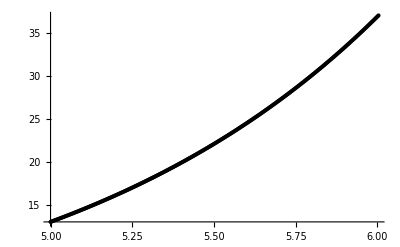

```mathematica
(*въвеждаме условието на задачата*)
a = 5.; b = 6;
x = a;
y = 13.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^5+17 ⅇ^x-ⅇ^x Log[26]+ⅇ^5 Log[1+x^2])/ⅇ^5
(*съставяме мрежата*)
n = 317;
h  = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ",k1," k2 = ",k2," k3 = ", k3, " k4 = ", k4,  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```